## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2_typeI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Build enzyme model

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};


inhibitionListSubset=inhibitionList[[{2,3,8,9}]];
customRatiosDataList={};

numFits=20;
simulateDataFlag="normal";
nSamples=Null;
paramScanList=Null;
```

```mathematica
{fittingData, filteredDataList, bestFitDetails,
{enzymeModelLocal, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub,
	allCatalyticReactions,nonCatalyticReactions, absoluteFlux, absoluteRateForward,
absoluteRateReverse, relativeRateForward, relativeRateReverse, 
	otherAbsoluteRatesForward, otherAbsoluteRatesReverse}}=
buildFullEnzymeModel[enzymeModel, rxn, pathMASSef, inputPath, outputPath, dataFileName, inhibitionList,inhibitionList, KeqList, kmList, 
					 s05List, kcatList,inhibitionList, activationList, otherParmsList,inhibitionListSubset,bufferInfo, ionCharge,
					 catalyticReactionsSetsList, otherMetsReverseZeroSub,  otherMetsForwardZeroSub,   customRatiosDataList, MWCFlag,
					simplifyFlag, simplifyMaxTime, nActiveSites, fitLabel, numFits, simulateDataFlag, nSamples, paramScanList];
```

{glyc3p^c→0,nadp^c→0}

{dhap^c→0,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{dhap^c→∞,nadph^c→∞}

prod inhib

Loading flux equation...

Added inhibition reactions:

{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating other relative rate forward equation...

Simplifying...

{prod_inhib_dhap,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{prod_inhib_nadph,dhap^c→0}

{glyc3p^c→∞,nadp^c→∞}

Generating other relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Configuring enzyme fits...

Running enzyme fit...

Evaluating fitness results...

ENd

## Evaluate fit results

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | haldaneRatio_1 | 0.525251 | 0.275889 | 0.0000168392 | 70.1634 | 0.000024 | 7.16078×10^-6
1 | relRateRev_nadph | 0.024432 | 0.000596921 | 0.00497305 | 5.47036 | 0.0909091 | 0.085936
1 | relRateRev_nadph | 0.0232309 | 0.000539674 | 0.00712567 | 5.20856 | 0.136807 | 0.129681
1 | relRateRev_nadph | 0.0215518 | 0.000464479 | 0.00971951 | 4.84136 | 0.20076 | 0.19104
1 | relRateRev_nadph | 0.0193367 | 0.000373909 | 0.0124001 | 4.35478 | 0.284747 | 0.272347
1 | relRateRev_nadph | 0.0166283 | 0.000276499 | 0.0145322 | 3.75642 | 0.386863 | 0.372331
1 | relRateRev_nadph | 0.0136076 | 0.000185167 | 0.0154235 | 3.08469 | 0.5 | 0.484577
1 | relRateRev_nadph | 0.0105658 | 0.000111637 | 0.0147368 | 2.40351 | 0.613137 | 0.5984
1 | relRateRev_nadph | 0.00780192 | 0.00006087 | 0.0127345 | 1.78042 | 0.715253 | 0.702518
1 | relRateRev_nadph | 0.00551544 | 0.0000304201 | 0.010086 | 1.26195 | 0.79924 | 0.789154
1 | relRateRev_nadph | 0.00376626 | 0.0000141847 | 0.00745336 | 0.863464 | 0.863193 | 0.85574
1 | relRateRev_nadph | 0.00250656 | 6.28282×10^-6 | 0.00523176 | 0.575493 | 0.909091 | 0.903859
1 | relRateRev_dhap | 0.0636965 | 0.00405724 | 0.0143607 | 15.7968 | 0.0909091 | 0.10527
1 | relRateRev_dhap | 0.0602378 | 0.00362859 | 0.0203545 | 14.8782 | 0.136807 | 0.157161
1 | relRateRev_dhap | 0.0554639 | 0.00307625 | 0.0273483 | 13.6224 | 0.20076 | 0.228108
1 | relRateRev_dhap | 0.0492732 | 0.00242785 | 0.0342102 | 12.0142 | 0.284747 | 0.318957
1 | relRateRev_dhap | 0.0418633 | 0.00175254 | 0.0391477 | 10.1193 | 0.386863 | 0.426011
1 | relRateRev_dhap | 0.0337986 | 0.00114235 | 0.0404663 | 8.09326 | 0.5 | 0.540466
1 | relRateRev_dhap | 0.0258809 | 0.000669823 | 0.0376494 | 6.14045 | 0.613137 | 0.650786
1 | relRateRev_dhap | 0.0188564 | 0.000355564 | 0.0317392 | 4.43749 | 0.715253 | 0.746992
1 | relRateRev_dhap | 0.0131629 | 0.000173262 | 0.0245947 | 3.07727 | 0.79924 | 0.823835
1 | relRateRev_dhap | 0.00887697 | 0.0000788007 | 0.0178252 | 2.06503 | 0.863193 | 0.881018
1 | relRateRev_dhap | 0.00582688 | 0.0000339526 | 0.0122794 | 1.35073 | 0.909091 | 0.92137
1 | relRateFor_nadp | 0.0301282 | 0.000907708 | 0.00609283 | 6.70211 | 0.0909091 | 0.0848163
1 | relRateFor_nadp | 0.0286577 | 0.000821266 | 0.00873606 | 6.38569 | 0.136807 | 0.128071
1 | relRateFor_nadp | 0.0266005 | 0.000707587 | 0.0119275 | 5.94119 | 0.20076 | 0.188832
1 | relRateFor_nadp | 0.0238839 | 0.000570443 | 0.0152368 | 5.35099 | 0.284747 | 0.26951
1 | relRateFor_nadp | 0.0205579 | 0.000422629 | 0.0178861 | 4.62335 | 0.386863 | 0.368977
1 | relRateFor_nadp | 0.016843 | 0.000283687 | 0.01902 | 3.804 | 0.5 | 0.48098
1 | relRateFor_nadp | 0.013096 | 0.000171505 | 0.018213 | 2.97046 | 0.613137 | 0.594924
1 | relRateFor_nadp | 0.00968603 | 0.0000938191 | 0.0157756 | 2.2056 | 0.715253 | 0.699477
1 | relRateFor_nadp | 0.00686122 | 0.0000470763 | 0.0125276 | 1.56744 | 0.79924 | 0.786712
1 | relRateFor_nadp | 0.00469784 | 0.0000220697 | 0.00928699 | 1.07589 | 0.863193 | 0.853906
1 | relRateFor_nadp | 0.00313856 | 9.85058×10^-6 | 0.00654614 | 0.720076 | 0.909091 | 0.902545
1 | relRateFor_glyc3p | 0.0562596 | 0.00316514 | 0.0125734 | 13.8308 | 0.0909091 | 0.103483
1 | relRateFor_glyc3p | 0.0528022 | 0.00278807 | 0.0176866 | 12.9281 | 0.136807 | 0.154493
1 | relRateFor_glyc3p | 0.0480301 | 0.00230689 | 0.023477 | 11.6941 | 0.20076 | 0.224237
1 | relRateFor_glyc3p | 0.0418417 | 0.00175073 | 0.0287988 | 10.1138 | 0.284747 | 0.313546
1 | relRateFor_glyc3p | 0.0344345 | 0.00118573 | 0.0319225 | 8.25164 | 0.386863 | 0.418786
1 | relRateFor_glyc3p | 0.0263726 | 0.000695516 | 0.0313035 | 6.26069 | 0.5 | 0.531303
1 | relRateFor_glyc3p | 0.0184577 | 0.000340688 | 0.0266203 | 4.34166 | 0.613137 | 0.639757
1 | relRateFor_glyc3p | 0.0114356 | 0.000130772 | 0.0190837 | 2.66811 | 0.715253 | 0.734336
1 | relRateFor_glyc3p | 0.00574386 | 0.000032992 | 0.0106407 | 1.33136 | 0.79924 | 0.809881
1 | relRateFor_glyc3p | 0.00145921 | 2.1293×10^-6 | 0.00290517 | 0.336561 | 0.863193 | 0.866098
1 | relRateFor_glyc3p | 0.00159014 | 2.52856×10^-6 | 0.0033225 | 0.365475 | 0.909091 | 0.905768
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0733169 | 0.00537536 | 0.0114941 | 18.3905 | 0.0625 | 0.0739941
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0618253 | 0.00382237 | 0.0266373 | 15.2989 | 0.174112 | 0.20075
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0394587 | 0.00155699 | 0.038045 | 9.51124 | 0.4 | 0.438045
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0133994 | 0.000179543 | 0.021253 | 3.13341 | 0.678269 | 0.699522
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00365409 | 0.0000133523 | 0.00728569 | 0.837855 | 0.869565 | 0.86228
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.103101 | 0.0106299 | 0.0127594 | 26.7948 | 0.047619 | 0.0603785
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0906248 | 0.00821286 | 0.0316797 | 23.204 | 0.136527 | 0.168207
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0642189 | 0.00412407 | 0.0531206 | 15.9362 | 0.333333 | 0.386454
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0293091 | 0.000859025 | 0.0427675 | 6.98161 | 0.612574 | 0.655342
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00356394 | 0.0000127017 | 0.0068667 | 0.824005 | 0.833333 | 0.8402
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.136152 | 0.0185372 | 0.0118776 | 36.8206 | 0.0322581 | 0.0441357
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.12453 | 0.0155077 | 0.0316662 | 33.2078 | 0.0953577 | 0.127024
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0972968 | 0.00946667 | 0.0627785 | 25.1114 | 0.25 | 0.312778
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.054549 | 0.0029756 | 0.0686786 | 13.3833 | 0.513167 | 0.581846
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0166358 | 0.000276749 | 0.0300372 | 3.90484 | 0.769231 | 0.799268
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0899888 | 0.00809799 | 0.00919823 | 18.7149 | 0.0491493 | 0.0399511
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0758582 | 0.00575446 | 0.0217916 | 16.0266 | 0.135972 | 0.11418
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0464142 | 0.00215428 | 0.0312246 | 10.136 | 0.308057 | 0.276832
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.008408 | 0.0000706944 | 0.009848 | 1.91739 | 0.513614 | 0.503766
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0189795 | 0.000360222 | 0.0290797 | 4.46709 | 0.650976 | 0.680056
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0701569 | 0.00492199 | 0.00590463 | 17.5322 | 0.0336788 | 0.0395834
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0693271 | 0.00480624 | 0.0164107 | 17.3078 | 0.0948165 | 0.111227
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0675974 | 0.00456941 | 0.0374898 | 16.8416 | 0.222603 | 0.260093
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0653696 | 0.00427319 | 0.0630153 | 16.2437 | 0.387936 | 0.450951
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.063772 | 0.00406687 | 0.080195 | 15.8169 | 0.50702 | 0.587215
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.274298 | 0.0752395 | 0.0182002 | 88.0607 | 0.0206677 | 0.0388679
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.252996 | 0.0640069 | 0.0466945 | 79.0589 | 0.0590629 | 0.105757
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.209689 | 0.0439695 | 0.0888594 | 62.0649 | 0.143172 | 0.232031
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.155707 | 0.0242446 | 0.112319 | 43.1221 | 0.260467 | 0.372785
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.117979 | 0.0139191 | 0.109729 | 31.2137 | 0.351541 | 0.461271
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.185104 | 0.0342634 | 0.0210319 | 34.7026 | 0.0606061 | 0.0395742
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.179334 | 0.0321608 | 0.054184 | 33.8293 | 0.160169 | 0.105985
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.169118 | 0.0286008 | 0.107514 | 32.2542 | 0.333333 | 0.225819
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.158674 | 0.0251776 | 0.155016 | 30.6054 | 0.506498 | 0.351482
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.15263 | 0.023296 | 0.179593 | 29.6329 | 0.606061 | 0.426467
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.152684 | 0.0233124 | 0.0134734 | 29.6416 | 0.0454545 | 0.0319811
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.15337 | 0.0235224 | 0.0357409 | 29.7527 | 0.120127 | 0.0843857
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.154567 | 0.0238908 | 0.0748648 | 29.9459 | 0.25 | 0.175135
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.155785 | 0.0242689 | 0.114502 | 30.1421 | 0.379873 | 0.265371
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.156578 | 0.0245168 | 0.137589 | 30.2697 | 0.454545 | 0.316956
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.117449 | 0.0137942 | 0.0071804 | 23.6953 | 0.030303 | 0.0231226
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.125258 | 0.0156895 | 0.0200652 | 25.0551 | 0.0800844 | 0.0600192
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.13852 | 0.0191878 | 0.0455152 | 27.3091 | 0.166667 | 0.121151
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.15142 | 0.022928 | 0.0745476 | 29.4365 | 0.253249 | 0.178701
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.15878 | 0.0252111 | 0.0927948 | 30.6223 | 0.30303 | 0.210235
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00166755 | 2.78072×10^-6 | 0.00023952 | 0.383231 | 0.0625 | 0.0622605
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00146937 | 2.15905×10^-6 | 0.000588089 | 0.337764 | 0.174112 | 0.173524
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00106801 | 1.14065×10^-6 | 0.000982467 | 0.245617 | 0.4 | 0.399018
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.000573071 | 3.2841×10^-7 | 0.000894415 | 0.131867 | 0.678269 | 0.677374
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.000232494 | 5.40537×10^-8 | 0.000465387 | 0.0535195 | 0.869565 | 0.8691
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0376071 | 0.0014143 | 0.00430731 | 9.04535 | 0.047619 | 0.0519264
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0339553 | 0.00115296 | 0.0111027 | 8.13226 | 0.136527 | 0.14763
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0259791 | 0.000674915 | 0.0205482 | 6.16445 | 0.333333 | 0.353882
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0149077 | 0.00022224 | 0.0213924 | 3.49222 | 0.612574 | 0.633967
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00635046 | 0.0000403283 | 0.0122749 | 1.47299 | 0.833333 | 0.845608
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0824398 | 0.00679632 | 0.00674315 | 20.9038 | 0.0322581 | 0.0390012
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0765604 | 0.0058615 | 0.0183831 | 19.278 | 0.0953577 | 0.113741
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0624792 | 0.00390365 | 0.0386817 | 15.4727 | 0.25 | 0.288682
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0395183 | 0.00156169 | 0.0488857 | 9.52627 | 0.513167 | 0.562053
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.018285 | 0.000334342 | 0.0330782 | 4.30017 | 0.769231 | 0.802309
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.036552 | 0.00133605 | 0.00548797 | 8.78075 | 0.0625 | 0.067988
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.027172 | 0.000738316 | 0.0112415 | 6.45645 | 0.174112 | 0.185354
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00878628 | 0.0000771986 | 0.00817487 | 2.04372 | 0.4 | 0.408175
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0128427 | 0.000164934 | 0.0197636 | 2.91384 | 0.678269 | 0.658505
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0271109 | 0.000735 | 0.0526231 | 6.05166 | 0.869565 | 0.816942
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.116331 | 0.013533 | 0.0146271 | 30.7168 | 0.047619 | 0.0622461
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0995498 | 0.00991015 | 0.0351722 | 25.7621 | 0.136527 | 0.171699
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0645586 | 0.00416781 | 0.0534229 | 16.0269 | 0.333333 | 0.386756
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0193005 | 0.000372509 | 0.0278374 | 4.54433 | 0.612574 | 0.640412
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0134147 | 0.000179955 | 0.025347 | 3.04164 | 0.833333 | 0.807986
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.217694 | 0.0473905 | 0.0209934 | 65.0796 | 0.0322581 | 0.0532515
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.195722 | 0.0383073 | 0.0542928 | 56.936 | 0.0953577 | 0.14965
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.146155 | 0.0213614 | 0.100022 | 40.0088 | 0.25 | 0.350022
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.072967 | 0.00532418 | 0.0938847 | 18.2952 | 0.513167 | 0.607052
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0119283 | 0.000142284 | 0.0214204 | 2.78465 | 0.769231 | 0.790651
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.132314 | 0.017507 | 0.0139141 | 26.2629 | 0.0529801 | 0.039066
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.10864 | 0.0118027 | 0.0320335 | 22.1319 | 0.144739 | 0.112706
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.059478 | 0.00353763 | 0.0409565 | 12.7989 | 0.32 | 0.279044
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.00396848 | 0.0000157488 | 0.00476024 | 0.917963 | 0.518565 | 0.523325
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0501429 | 0.00251431 | 0.0789598 | 12.2388 | 0.645161 | 0.724121
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0230219 | 0.000530008 | 0.00193007 | 5.16294 | 0.0373832 | 0.0354531
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.00607817 | 0.0000369441 | 0.00143936 | 1.3898 | 0.103566 | 0.102126
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0297704 | 0.000886279 | 0.0166948 | 7.09531 | 0.235294 | 0.251989
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0772948 | 0.00597448 | 0.0766752 | 19.4799 | 0.393613 | 0.470288
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.112924 | 0.0127518 | 0.148476 | 29.6952 | 0.5 | 0.648476
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.104338 | 0.0108864 | 0.00638972 | 27.1563 | 0.0235294 | 0.0299191
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.114808 | 0.0131808 | 0.0199741 | 30.259 | 0.0660105 | 0.0859846
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.137324 | 0.0188577 | 0.0572159 | 37.1903 | 0.153846 | 0.211062
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.167963 | 0.0282117 | 0.125418 | 47.2188 | 0.265611 | 0.391029
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.191891 | 0.0368221 | 0.191578 | 55.5575 | 0.344828 | 0.536405
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.777644 | 0.60473 | 0.0482396 | 83.3139 | 0.0579011 | 0.00966146
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.727559 | 0.529342 | 0.126115 | 81.2742 | 0.155173 | 0.0290573
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.619096 | 0.383279 | 0.251459 | 75.9617 | 0.331034 | 0.0795752
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.46525 | 0.216458 | 0.339197 | 65.743 | 0.515944 | 0.176747
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.337718 | 0.114053 | 0.338697 | 54.0503 | 0.626632 | 0.287935
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.660853 | 0.436727 | 0.033203 | 78.1653 | 0.0424779 | 0.00927491
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.624751 | 0.390314 | 0.0874025 | 76.2727 | 0.114592 | 0.0271896
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.549206 | 0.301627 | 0.177562 | 71.7646 | 0.247423 | 0.0698609
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.449684 | 0.202216 | 0.251909 | 64.4928 | 0.390601 | 0.138691
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.375323 | 0.140867 | 0.276629 | 57.8617 | 0.478088 | 0.201458
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.508815 | 0.258893 | 0.0191259 | 69.0126 | 0.0277136 | 0.00858772
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.494563 | 0.244593 | 0.0511468 | 67.9789 | 0.0752393 | 0.0240925
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.4665 | 0.217622 | 0.108232 | 65.8414 | 0.164384 | 0.0561512
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.433227 | 0.187686 | 0.165931 | 63.1215 | 0.262875 | 0.0969442
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.411098 | 0.169002 | 0.198466 | 61.1937 | 0.324324 | 0.125858
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0888792 | 0.00789951 | 0.0141936 | 22.7098 | 0.0625 | 0.0766936
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0772932 | 0.00597424 | 0.0339161 | 19.4794 | 0.174112 | 0.208029
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0547502 | 0.00299758 | 0.0537432 | 13.4358 | 0.4 | 0.453743
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0284977 | 0.00081212 | 0.0459996 | 6.78192 | 0.678269 | 0.724268
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.011329 | 0.000128345 | 0.0229818 | 2.64291 | 0.869565 | 0.892547
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0740299 | 0.00548042 | 0.00885001 | 18.585 | 0.047619 | 0.0564691
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0665596 | 0.00443018 | 0.0226126 | 16.5627 | 0.136527 | 0.15914
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0504667 | 0.00254688 | 0.0410749 | 12.3225 | 0.333333 | 0.374408
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0286102 | 0.000818546 | 0.0417138 | 6.80959 | 0.612574 | 0.654288
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0120775 | 0.000145867 | 0.0234999 | 2.81998 | 0.833333 | 0.856833
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0592115 | 0.003506 | 0.00471196 | 14.6071 | 0.0322581 | 0.03697
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0550947 | 0.00303543 | 0.0128979 | 13.5258 | 0.0953577 | 0.108256
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0451675 | 0.0020401 | 0.0274007 | 10.9603 | 0.25 | 0.277401
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0287783 | 0.000828193 | 0.0351568 | 6.85094 | 0.513167 | 0.548324
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0134041 | 0.00017967 | 0.0241118 | 3.13453 | 0.769231 | 0.793343

### Simulated Data and Best Fit Data Plot

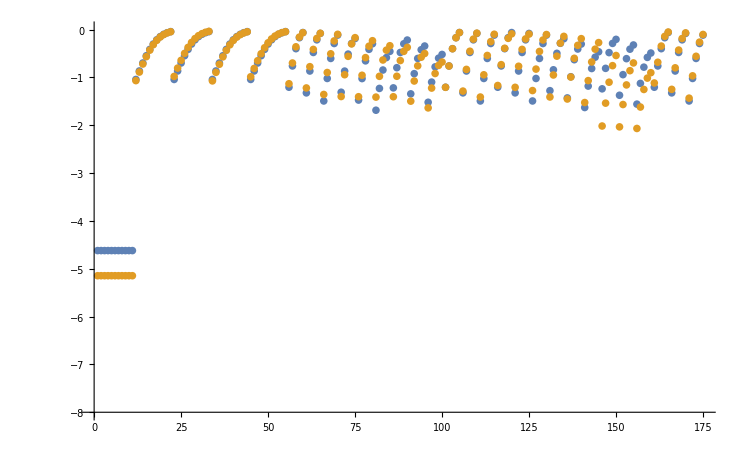

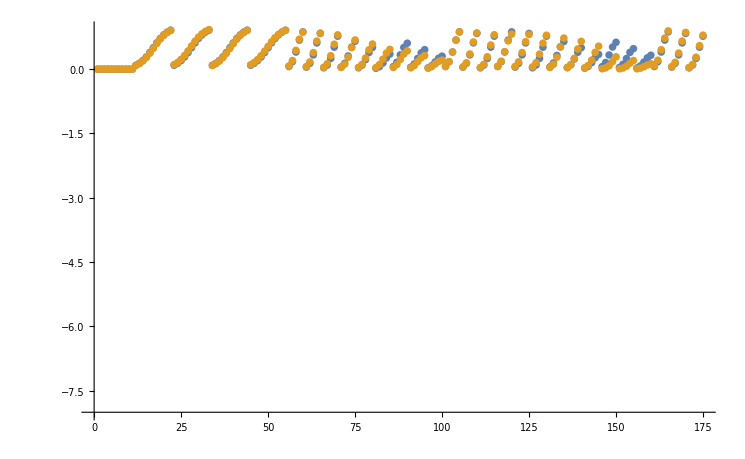

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

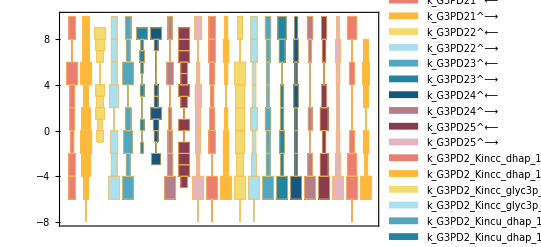

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

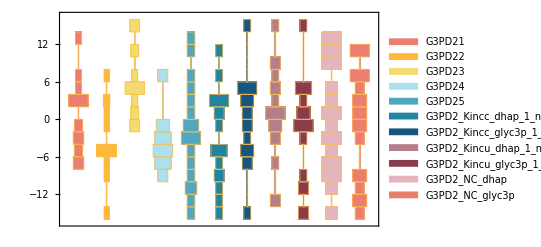

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

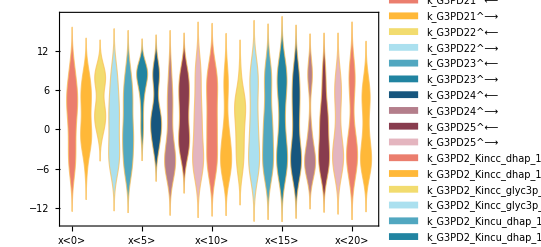

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

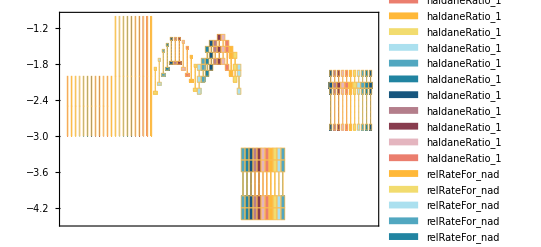

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Power::infy: Infinite expression 1/0. encountered.

data value | predicted value | error in %
3.4×10^-6 | 3.61643×10^-6 | 6.36544
0.00018 |  | 
0.000165 | 0.000178023 | 7.89283
0.00003 |  |

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000024 | 7.16078×10^-6 | 70.1634